```mathematica
SetDirectory[NotebookDirectory[]]
If[!DirectoryQ["plots"],CreateDirectory["plots"]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.;
ωmax=4.;
Amin=0.0;
Amax=0.1;
M=16;
M2=3;
κ=1;
η=0.1;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]

A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(ω^2*2*I*n+ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1+(-1)^j*Δ)*Cos[q/2]*(KroneckerDelta[i,j+1]+KroneckerDelta[i,j-1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]

A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1-(-1)^i*Δ)*Cos[q/2]*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];

findroot[a0_,ω_,Δ_,q_]:=Module[{g,a},g[a_?NumericQ]:=Max[Re[Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]]];
{a,g[a]}/.FindRoot[g[a],{a,a0}]]
```

/home/zack/Desktop

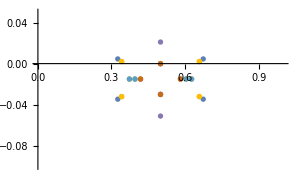
-Graphics- | {0.725212,0.804272,0.804272,0.817129,0.817129,0.817129,0.817129,0.827668,0.827668,0.828717,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.909769,0.998748,1.00001,1.00001,1.01291,1.01291,1.01291,1.01291,1.0291,1.0291,1.14129}

```mathematica
f[a_,ω_,Δ_,q_]:=Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]
a=0.0975238;
ω=3.32215;
Grid[{{ListPlot[Table[{Im[#],Re[#]}&/@f[a,ω,0.35,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}],PlotRange->{{0,1},{-0.1,0.05}},ImageSize->300],
Sort[Abs[Exp[2*Pi*Flatten[Table[f[a,ω,0.35,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}]]]]]}}]
```

{31.5183,Null}

{1.6436,Null}

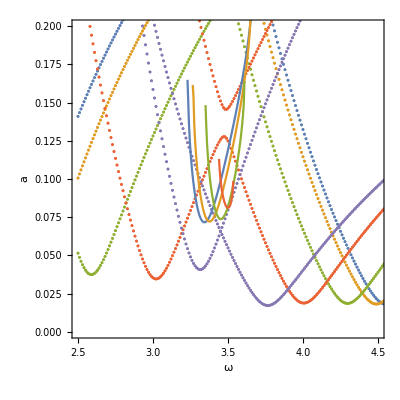

```mathematica
Δ=0.35;

tongues={};
ω0=3.4;
a0=0.08;
ωmin=2.5;
ωmax=5.0;

AbsoluteTiming[Monitor[Do[tongue={};
a=a0;
ω=ω0;
continue=True;While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω+dω;If[ω>ωmax||Abs[err]>10^-6,continue=False]; {ω-dω,a,err}];];
a=a0;
ω=ω0;
continue=True;
While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω-dω;If[ω<ωmin||Abs[err]>10^-6,continue=False]; {ω+dω,a,err}];];
AppendTo[tongues,tongue];{ω0,a0}=(First@MinimalBy[tongue,#[[2]]&])[[{1,2}]];,{q,0,Pi-4*Pi/M,4*Pi/M}],{ω,q}]]

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,Pi,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[i]]]],{i,1,Length[pds]}],PlotRange->{0,0.2}];
Show[p0,ListPlot[SortBy[#,#[[1]]&]&/@tongues[[All,All,{1,2}]],Joined->True],PlotRange->{{2.5,4.5},{0,0.2}},Axes->False,Frame->True,FrameLabel->{"ω","a"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

```mathematica
a0
```

0.37864

{11.0828,Null}

{0.940622,Null}

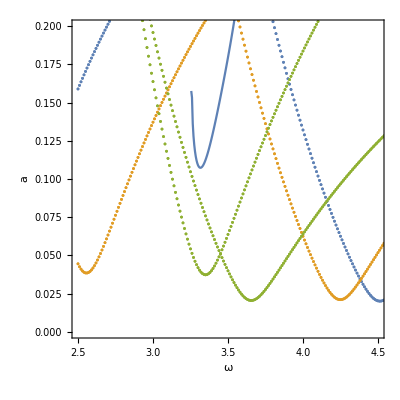

```mathematica
Δ=0.25;

tongues={};
ω0=3.3;
a0=0.1;
ωmin=2.5;
ωmax=5.0;
M=8;

AbsoluteTiming[Monitor[Do[tongue={};
a=a0;
ω=ω0;
continue=True;While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω+dω;If[ω>ωmax||Abs[err]>10^-6,continue=False]; {ω-dω,a,err}];];
a=a0;
ω=ω0;
continue=True;
While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω-dω;If[ω<ωmin||Abs[err]>10^-6,continue=False]; {ω+dω,a,err}];];
AppendTo[tongues,tongue];{ω0,a0}=(First@MinimalBy[tongue,#[[2]]&])[[{1,2}]];,{q,0,Pi-4*Pi/M,4*Pi/M}],{ω,q}]]

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,Pi,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[i]]]],{i,1,Length[pds]}],PlotRange->{0,0.2}];
Show[p0,ListPlot[SortBy[#,#[[1]]&]&/@tongues[[All,All,{1,2}]],Joined->True],PlotRange->{{2.5,4.5},{0,0.2}},Axes->False,Frame->True,FrameLabel->{"ω","a"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

```mathematica
Cases[Flatten[pds,2],u_/;u[[1]]==3.5]
```

{{3.5,0,0.347553},{3.5,0,0.347553},{3.5,0,0.306832},{3.5,0,0.306832},{3.5,π/2,0.239733},{3.5,π/2,0.239733},{3.5,π/2,0.223424},{3.5,π/2,0.223424},{3.5,π,0.0637276},{3.5,π,0.0637276},{3.5,π,0.0399428},{3.5,π,0.0399428}}

```mathematica
Cases[Flatten[tongues,1],u_/;u[[1]]==3.5]
```

{{3.5,0.179578,5.92328×10^-15}}

```mathematica
tongues
```

{{{3.3,0.109033,-1.3254×10^-15},{3.305,0.108102,-3.53544×10^-15},{3.31,0.10755,-4.55658×10^-15},{3.315,0.107331,5.19702×10^-15},{3.32,0.107405,2.78311×10^-15},{3.325,0.10774,-1.6312×10^-15},{3.33,0.108307,-1.4927×10^-15},{3.335,0.109079,-4.53918×10^-15},{3.34,0.110036,6.33561×10^-15},{3.345,0.111158,-2.63894×10^-15},{3.35,0.112426,3.49608×10^-15},{3.355,0.113826,4.39342×10^-15},{3.36,0.115345,2.05077×10^-15},{3.365,0.116968,-3.39681×10^-15},{3.37,0.118687,-7.06252×10^-16},{3.375,0.12049,3.56378×10^-15},{3.38,0.12237,-2.10283×10^-15},{3.385,0.124319,2.60325×10^-15},{3.39,0.12633,-1.97286×10^-15},{3.395,0.128397,2.86428×10^-15},{3.4,0.130515,-2.66769×10^-15},{3.405,0.13268,-3.94157×10^-15},{3.41,0.134886,2.63749×10^-15},{3.415,0.137132,1.63505×10^-15},{3.42,0.139413,-4.45172×10^-16},{3.425,0.141727,-4.44418×10^-16},{3.43,0.144072,8.23941×10^-16},{3.435,0.146446,-9.06887×10^-15},{3.44,0.148847,-1.45271×10^-15},{3.445,0.151274,-2.29084×10^-15},{3.45,0.153726,5.26589×10^-15},{3.455,0.156203,-2.21984×10^-15},{3.46,0.158703,1.73501×10^-15},{3.465,0.161227,2.4412×10^-15},{3.47,0.163774,-5.66904×10^-15},{3.475,0.166345,-1.63381×10^-16},{3.48,0.16894,7.52728×10^-15},{3.485,0.17156,4.79883×10^-15},{3.49,0.174205,-2.94607×10^-15},{3.495,0.176878,-1.46055×10^-15},{3.5,0.179578,5.92328×10^-15},{3.505,0.182309,-1.29404×10^-15},{3.51,0.185071,9.33947×10^-15},{3.515,0.187868,-3.23319×10^-15},{3.52,0.190702,-2.46936×10^-15},{3.525,0.193577,-1.14954×10^-17},{3.53,0.196497,7.24753×10^-15},{3.535,0.199465,-5.38355×10^-16},{3.54,0.202489,-4.06357×10^-15},{3.545,0.205574,-3.22193×10^-15},{3.55,0.208728,9.46074×10^-16},{3.555,0.211961,3.38686×10^-15},{3.56,0.215284,-2.63055×10^-15},{3.565,0.218714,-7.04713×10^-16},{3.57,0.222268,6.01881×10^-15},{3.575,0.225974,1.99173×10^-16},{3.58,0.229865,2.48372×10^-15},{3.585,0.233993,-1.36671×10^-15},{3.59,0.238434,1.12093×10^-15},{3.595,0.243317,9.89262×10^-15},{3.6,0.24889,-2.0937×10^-15},{3.605,0.255781,-2.49215×10^-15},{3.61,0.268285,-1.29824×10^-14},{3.615,0.268049,-0.00553293},{3.3,0.109033,-1.3254×10^-15},{3.295,0.110402,-3.45033×10^-16},{3.29,0.112284,3.89726×10^-15},{3.285,0.11478,-5.51477×10^-16},{3.28,0.118037,-7.67097×10^-15},{3.275,0.122296,-1.89392×10^-15},{3.27,0.128,-3.7391×10^-16},{3.265,0.136232,-8.56302×10^-15},{3.26,0.153259,-1.1633×10^-15},{3.255,0.157585,-0.000842779}},{{3.315,0.107331,-0.015083},{3.315,0.107331,-0.015083}}}